## First some definitions

```mathematica
DerivedPossibilities[sets_,new_]:=Block[{
results={},
temp},
Table[
temp=sets;
temp[[1,pos1]]=Append[temp[[1,pos1]],new];
temp[[2,pos2]]=Append[temp[[2,pos2]],new];
temp[[3,pos3]]=Append[temp[[3,pos3]],new];
temp[[4,pos4]]=Append[temp[[4,pos4]],new];
temp[[5,pos5]]=Append[temp[[5,pos5]],new];
AppendTo[results,temp]
,{pos1,4},{pos2,4},{pos3,4},{pos4,4},{pos5,4}];
results
]
```

```mathematica
IsCoreShape[set_,nodes_]:=(Length[set]==nodes-1&&(MemberQ[set,{1,3}]||MemberQ[set,{1,4}]||MemberQ[set,{2,4}]||MemberQ[set,{2,5}]||MemberQ[set,{3,5}])) ||(Length[set]==nodes-2&&(
(MemberQ[set,{1,3}]&&MemberQ[set,{2,5}])
||(MemberQ[set,{1,3}]&&MemberQ[set,{2,4}])
||(MemberQ[set,{1,4}]&&MemberQ[set,{2,5}])
||(MemberQ[set,{1,4}]&&MemberQ[set,{3,5}])
||(MemberQ[set,{2,4}]&&MemberQ[set,{3,5}])

))
```

```mathematica
MyFormatSymbol[sym_,goodValue_]:=With[{s=SymbolToSets[sym]
},
With[{nodes=Length[Flatten[s]]},
If[IsCoreShape[s,nodes],
Framed[ColorShape2[ s],Background->Yellow],
If[MemberQ[goodValue,s],
Framed[ColorShape2[ s],Background->LightYellow],
ColorShape2[ s]
],ColorShape2[ s]]
]
]
```

```mathematica
ColorShape2[sets_]:=Style[SetsToLabel[sets],If[HasQuadrilateralPattern[sets],Darker[Green],If[HasTrianglePattern[sets],Red,Black]]]
```

```mathematica
WriteFormula[sets_]:=Map[MyFormatSymbol[#,7]&,Select[FindFullFormula[GraphFromPatterns[sets]],SymbolLevel[#]==4&]]
```

## Now we start calculating

```mathematica
start7={{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}},{{1,6},{2,7},{3,5},{4}},{{1,4},{2,6},{3,7},{5}},{{1,6},{2,5},{3,7},{4}}};
```

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],7]&,start7]
```

{13♁26♁47♁5,16♁24♁37♁5,16♁27♁35♁4,14♁26♁37♁5,16♁25♁37♁4}

```mathematica
WriteFormula[start7]
```

{1♁26♁35♁47,1♁247♁35♁6,16♁2♁35♁47,16♁27♁35♁4,16♁25♁3♁47,16♁25♁37♁4,16♁247♁3♁5,16♁24♁37♁5,16♁24♁35♁7,14♁27♁35♁6,14♁26♁37♁5,14♁26♁35♁7,14♁25♁37♁6,13♁26♁47♁5,13♁25♁47♁6,13♁247♁5♁6}

```mathematica
Select[DerivedPossibilities[start7,8],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ==0&]
```

{}

## Eight is on

```mathematica
sols8=Select[DerivedPossibilities[start7,8],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ≤2&]
```

{{{{1,3},{2,6},{4,7},{5,8}},{{1,6},{2,4},{3,7},{5,8}},{{1,6},{2,7},{3,5},{4,8}},{{1,4},{2,6},{3,7},{5,8}},{{1,6},{2,5},{3,7},{4,8}}}}

```mathematica
start8=First[sols8]
```

{{{1,3},{2,6},{4,7},{5,8}},{{1,6},{2,4},{3,7},{5,8}},{{1,6},{2,7},{3,5},{4,8}},{{1,4},{2,6},{3,7},{5,8}},{{1,6},{2,5},{3,7},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],8]&,start8]
```

{13♁26♁47♁58,16♁24♁37♁58,16♁27♁35♁48,14♁26♁37♁58,16♁25♁37♁48}

```mathematica
WriteFormula[start8]
```

{16♁27♁35♁48,16♁25♁37♁48,16♁247♁3♁58,16♁24♁37♁58,16♁247♁35♁8,14♁26♁37♁58,13♁26♁47♁58,13♁247♁58♁6}

## Nine is on

```mathematica
Select[DerivedPossibilities[start8,9],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ==0&]
```

{}

```mathematica
sols9=Select[DerivedPossibilities[start8,9],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ≤1&]
```

{{{{1,3,9},{2,6},{4,7},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5},{4,8}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}},{{{1,3},{2,6,9},{4,7},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5},{4,8}},{{1,4},{2,6,9},{3,7},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}},{{{1,3},{2,6,9},{4,7},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5},{4,8}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}},{{{1,3},{2,6},{4,7,9},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7},{3,5,9},{4,8}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}},{{{1,3},{2,6},{4,7,9},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7},{3,5},{4,8,9}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}},{{{1,3},{2,6},{4,7,9},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7},{3,5},{4,8,9}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7},{4,8,9}}}}

```mathematica
start9=First[sols9]
```

{{{1,3,9},{2,6},{4,7},{5,8}},{{1,6},{2,4},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5},{4,8}},{{1,4},{2,6},{3,7,9},{5,8}},{{1,6},{2,5},{3,7,9},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],9]&,start9]
```

{139♁26♁47♁58,16♁24♁379♁58,16♁279♁35♁48,14♁26♁379♁58,16♁25♁379♁48}

```mathematica
WriteFormula[start9]
```

{16♁279♁35♁48,16♁25♁379♁48,16♁247♁39♁58,16♁24♁379♁58,14♁26♁379♁58,139♁26♁47♁58,139♁247♁58♁6}

## Ten is on

```mathematica
WriteFormula[{{{1,3,9,10},{2,6},{4,7},{5,8}},{{1,6},{2,4,10},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8}},{{1,4,10},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10},{3,7,9},{4,8}}}]
```

{16♁279♁35a♁48,16♁25a♁379♁48,16♁247♁39a♁58,16♁24a♁379♁58,14a♁26♁379♁58,139a♁26♁47♁58,139a♁247♁58♁6}

```mathematica
Select[DerivedPossibilities[start9,10],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ==0&]
```

{{{{1,3,9},{2,6},{4,7,10},{5,8}},{{1,6},{2,4},{3,7,9,10},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8}},{{1,4},{2,6},{3,7,9,10},{5,8}},{{1,6},{2,5},{3,7,9,10},{4,8}}},{{{1,3,9},{2,6},{4,7,10},{5,8}},{{1,6},{2,4},{3,7,9,10},{5,8}},{{1,6},{2,7,9},{3,5},{4,8,10}},{{1,4},{2,6},{3,7,9,10},{5,8}},{{1,6},{2,5},{3,7,9,10},{4,8}}},{{{1,3,9},{2,6},{4,7,10},{5,8}},{{1,6},{2,4},{3,7,9,10},{5,8}},{{1,6},{2,7,9},{3,5},{4,8,10}},{{1,4},{2,6},{3,7,9,10},{5,8}},{{1,6},{2,5},{3,7,9},{4,8,10}}}}

```mathematica
zero10={{{1,3,9},{2,6},{4,7,10},{5,8}},{{1,6},{2,4},{3,7,9,10},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8}},{{1,4},{2,6},{3,7,9,10},{5,8}},{{1,6},{2,5},{3,7,9,10},{4,8}}}
```

{{{1,3,9},{2,6},{4,7,10},{5,8}},{{1,6},{2,4},{3,7,9,10},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8}},{{1,4},{2,6},{3,7,9,10},{5,8}},{{1,6},{2,5},{3,7,9,10},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],10]&,zero10]
```

{139♁26♁47a♁58,16♁24♁379a♁58,16♁279♁35a♁48,14♁26♁379a♁58,16♁25♁379a♁48}

```mathematica
WriteFormula[zero10]
```

{16♁279♁35a♁48,16♁25♁379a♁48,16♁247♁39a♁58,16♁24♁379a♁58,14♁26♁379a♁58,139♁26♁47a♁58}

```mathematica
MatrixForm[AdjacencyMatrix[GraphFromPatterns[zero10]],TableHeadings->{Range[10],Range[10]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1
3 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
4 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0
5 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
6 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
7 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0
8 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
9 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
10 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

```mathematica
MatrixRank[AdjacencyMatrix[GraphFromPatterns[zero10]]]
```

8

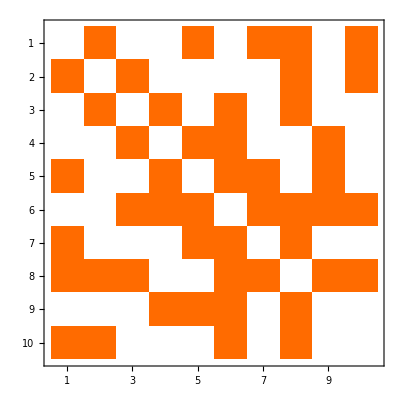

```mathematica
MatrixPlot[AdjacencyMatrix[GraphFromPatterns[zero10]]]
```

```mathematica
EdgeCount[GraphFromPatterns[zero10]]
```

24

```mathematica
3*10-6
```

24

```mathematica
FindClique[GraphFromPatterns[zero10]]
```

{{1,2,8,10}}

```mathematica
sols10=Select[DerivedPossibilities[start9,10],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ≤1&]
```

$Aborted

```mathematica
start10=First[sols10]
```

{{{1,3,9,10},{2,6},{4,7},{5,8}},{{1,6},{2,4,10},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8}},{{1,4,10},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10},{3,7,9},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],10]&,start10]
```

{13910♁26♁47♁58,16♁2410♁379♁58,16♁279♁3510♁48,1410♁26♁379♁58,16♁2510♁379♁48}

```mathematica
WriteFormula[start10]
```

{16♁279♁3510♁48,16♁2510♁379♁48,16♁247♁3910♁58,16♁2410♁379♁58,1410♁26♁379♁58,13910♁26♁47♁58,13910♁247♁58♁6}

## Eleven is

```mathematica
Select[DerivedPossibilities[start10,11],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ==0&]
```

{{{{1,3,9,10},{2,6},{4,7,11},{5,8}},{{1,6},{2,4,10},{3,7,9,11},{5,8}},{{1,6},{2,7,9},{3,5,10,11},{4,8}},{{1,4,10},{2,6},{3,7,9,11},{5,8}},{{1,6},{2,5,10},{3,7,9,11},{4,8}}},{{{1,3,9,10},{2,6},{4,7,11},{5,8}},{{1,6},{2,4,10},{3,7,9,11},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8,11}},{{1,4,10},{2,6},{3,7,9,11},{5,8}},{{1,6},{2,5,10},{3,7,9,11},{4,8}}},{{{1,3,9,10},{2,6},{4,7,11},{5,8}},{{1,6},{2,4,10},{3,7,9,11},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8,11}},{{1,4,10},{2,6},{3,7,9,11},{5,8}},{{1,6},{2,5,10},{3,7,9},{4,8,11}}}}

```mathematica
zero11={{{1,3,9,10},{2,6},{4,7,11},{5,8}},{{1,6},{2,4,10},{3,7,9,11},{5,8}},{{1,6},{2,7,9},{3,5,10,11},{4,8}},{{1,4,10},{2,6},{3,7,9,11},{5,8}},{{1,6},{2,5,10},{3,7,9,11},{4,8}}};
```

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],11]&,zero11]
```

{13910♁26♁4711♁58,16♁2410♁37911♁58,16♁279♁351011♁48,1410♁26♁37911♁58,16♁2510♁37911♁48}

```mathematica
VertexList[GraphFromPatterns[zero11]]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
MatrixForm[AdjacencyMatrix[GraphFromPatterns[zero11]],TableHeadings->{Range[11],Range[11]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1
2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
3 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
4 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
5 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
6 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
7 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0
8 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
9 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
11 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0)

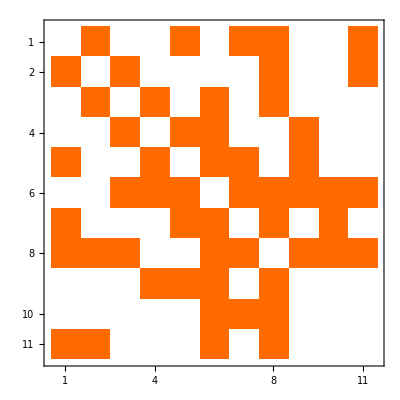

```mathematica
MatrixPlot[AdjacencyMatrix[GraphFromPatterns[zero11]]]
```

```mathematica
WriteFormula[zero11]
```

{16♁279♁351011♁48,16♁2510♁37911♁48,16♁247♁391011♁58,16♁2410♁37911♁58,1410♁26♁37911♁58,13910♁26♁4711♁58}

```mathematica
sols11=Select[DerivedPossibilities[start10,11],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ≤1&]
```

{{{{1,3,9,10,11},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10,11},{4,8}},{{1,4,10,11},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10,11},{3,7,9},{4,8}}},{{{1,3,9,10,11},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10},{4,8,11}},{{1,4,10,11},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10},{3,7,9},{4,8,11}}},149,{{{1,3,9,10},{2,6},{4,7},{5,8,11}},{{1,6},{2,4,10},{3,7,9},{5,8,11}},{{1,6},{2,7,9},{3,5,10},{4,8,11}},{{1,4,10},{2,6},{3,7,9},{5,8,11}},{{1,6},{2,5,10},{3,7,9,11},{4,8}}},{{{1,3,9,10},{2,6},{4,7},{5,8,11}},{{1,6},{2,4,10},{3,7,9},{5,8,11}},{{1,6},{2,7,9},{3,5,10},{4,8,11}},{{1,4,10},{2,6},{3,7,9},{5,8,11}},{{1,6},{2,5,10},{3,7,9},{4,8,11}}}}
 |  |  |  |

```mathematica
start11=First[sols11]
```

{{{1,3,9,10,11},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10,11},{4,8}},{{1,4,10,11},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10,11},{3,7,9},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],11]&,start11]
```

{1391011♁26♁47♁58,16♁241011♁379♁58,16♁279♁351011♁48,141011♁26♁379♁58,16♁251011♁379♁48}

```mathematica
WriteFormula[start11]
```

{16♁279♁351011♁48,16♁251011♁379♁48,16♁247♁391011♁58,16♁241011♁379♁58,141011♁26♁379♁58,1391011♁26♁47♁58,1391011♁247♁58♁6}

## And now for 12

```mathematica
sols12=Select[DerivedPossibilities[start11,12],Length[Select[FindFullFormula[GraphFromPatterns[#]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]] ≤1&]
```

{{{{1,3,9,10,11,12},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11,12},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10,11,12},{4,8}},{{1,4,10,11,12},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10,11,12},{3,7,9},{4,8}}},{{{1,3,9,10,11,12},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11,12},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10,11},{4,8,12}},{{1,4,10,11,12},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10,11},{3,7,9},{4,8,12}}},150,{{{1,3,9,10,11},{2,6},{4,7},{5,8,12}},{{1,6},{2,4,10,11},{3,7,9},{5,8,12}},{{1,6},{2,7,9},{3,5,10,11},{4,8,12}},{{1,4,10,11},{2,6},{3,7,9},{5,8,12}},{{1,6},{2,5,10,11},{3,7,9},{4,8,12}}}}
 |  |  |  |

```mathematica
start12=First[sols12]
```

{{{1,3,9,10,11,12},{2,6},{4,7},{5,8}},{{1,6},{2,4,10,11,12},{3,7,9},{5,8}},{{1,6},{2,7,9},{3,5,10,11,12},{4,8}},{{1,4,10,11,12},{2,6},{3,7,9},{5,8}},{{1,6},{2,5,10,11,12},{3,7,9},{4,8}}}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],12]&,start12]
```

{139101112♁26♁47♁58,16♁24101112♁379♁58,16♁279♁35101112♁48,14101112♁26♁379♁58,16♁25101112♁379♁48}

```mathematica
WriteFormula[start12]
```

{16♁279♁35101112♁48,16♁25101112♁379♁48,16♁247♁39101112♁58,16♁24101112♁379♁58,14101112♁26♁379♁58,139101112♁26♁47♁58,139101112♁247♁58♁6}